```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
n=First@Import["numbOfMeshLevels.dat","List"]
```

2

```mathematica
n=1
```

1

## Meshes

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
𝒯=Table[import["meshes/"<>ToString@i<>"_mesh.ntr"],{i,0,n}];
```

```mathematica
Show[highlight[#,{"ribsNumn","localNodesNumn","nodesNumn","trianglesNumn"}]&/@𝒯//GraphicsRow,ImageSize->Full]
```

-Graphics-

## Prolongation / Restriction Sparse Matrices

```mathematica
R=Table[Import["operators/"<>ToString@i<>"_R.rra"],{i,n}];
```

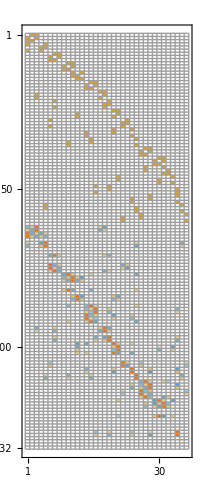

```mathematica
Show[MatrixPlot[Transpose@#,MaxPlotPoints->∞,Mesh->All]&/@R//GraphicsRow,ImageSize->Full]
```

## Interpolants

### Set DOFs on the Coarsest Mesh

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/FEinterpolants.nb"]
```

```mathematica
u@{x_,y_}:=x(x-1)^2 y(y-1)^4
```

```mathematica
uPlot=Plot3D[u@{x,y},{x,y}∈region@First@𝒯,Mesh->None]
```

-Graphics3D-

```mathematica
ξ=𝒫ξ=Table[{},{i,0,n}];
ξ[[1]]=computeDOFs[u,ΔP1CR,First@𝒯];
𝒫ξ[[1]]=𝒫[First@ξ,ΔP1CR,First@𝒯];
```

```mathematica
Show[GraphicsRow@{uPlot,plot𝒫ξ[First@𝒫ξ,First@𝒯]},ImageSize->Full]
```

-Graphics-

### Prolongate

```mathematica
Do[
ξ[[i+1]]=Transpose@R[[i]].ξ[[i]];
𝒫ξ[[i+1]]=𝒫[ξ[[i+1]],ΔP1CR,𝒯[[i+1]]]
,{i,n}]
```

```mathematica
colors=ColorData[3,"ColorList"][[2;;]];
Show[MapIndexed[plot𝒫ξ[#1,𝒯[[First@#2]],{colors[[First@#2]],Opacity@.8}]&,𝒫ξ](*//GraphicsRow*),ImageSize->Full]
```

-Graphics3D-

### Set DOFs on the Fines Mesh

```mathematica
η=𝒫η=Table[{},{i,0,n}];
η[[n+1]]=computeDOFs[u,ΔP1CR,Last@𝒯];
𝒫η[[n+1]]=𝒫[Last@η,ΔP1CR,Last@𝒯];
```

### Restrict

```mathematica
Do[
η[[i]]=R[[i]].η[[i+1]];
𝒫η[[i]]=𝒫[η[[i]],ΔP1CR,𝒯[[i]]]
,{i,n,1,-1}]
```

```mathematica
Show[Reverse@MapIndexed[plot𝒫ξ[#1,𝒯[[First@#2]],{colors[[First@#2]],Opacity@.8}]&,𝒫η](*//GraphicsRow*),ImageSize->Full]
```

-Graphics3D-

## Drafts

```mathematica
Norm[η[[1]]-ξ[[1]]]
```

0.0706767

```mathematica
(%143)/(Norm@η[[1]])
```

3.73443

```mathematica
ξ[[1]]
```

{0.0082598,0.,0.0114663,0.,0.00742819,0.00141021,0.00521195,0.,0.,0.000697613,0.0000411066,0.0000570644,0.,0.00214305,0.00457312,0.00762018,0.,0.0100905,0.00917799,0.000640759,0.0000462,0.00126823,0.,0.00140407,0.00375166,0.000640528,0.000119105,0.00188305,0.,0.0000259384,7.01821×10^-6,0.,0.,0.00499253,0.,0.}

```mathematica
plotBasis[ΔP1L,First@𝒯,16]
```

-Graphics3D-

```mathematica
plotBasis[ΔP1CR,First@𝒯,27]
```

-Graphics3D-

```mathematica
plotShapes[ΔP1CR,First@𝒯,11]
```

-Graphics3D-